```mathematica
Clear[f1,g,h,i,j,f3,f,c,d,c1,d1,t,x,x1,x3,x4]
f[t_]:=1/(1+2t)
t1=f[t]/.t-> a;
t2=f[t]/.t-> b;
t3=D[f[t]];
f1[t_]:=Exp[-x t]
f3[t_]:=Exp[-x t]/(1+2t)
```

```mathematica
(*3 terms approximation integration by parts, taking into account that the boundary at Infinite should be neglected as we can see above*)
```

```mathematica
x4[0]=D[f[t],t]
```

-2/(1+2 t)^2

```mathematica
x3[0]=Integrate[f1[t],t]
```

-ⅇ^(-t x)/x

```mathematica
For[i=0,i<4,i++,x3[i+1]=Integrate[x3[i],t]];
```

```mathematica
For[i=0,i<4,i++,x4[i+1]=D[x4[i],t]];
```

```mathematica
x4[1]
```

8/(1+2 t)^3

```mathematica
Do[Print[-(f[a] x3[j]/.t-> a)+((x4[j]x3[j+1])/.t-> a )+((x4[j+1]x3[j+2])/.t-> a)],{j,0,3}]
```

-(8 ⅇ^(-a x))/((1+2 a)^3 x^3)-(2 ⅇ^(-a x))/((1+2 a)^2 x^2)+ⅇ^(-a x)/((1+2 a) x)

-(48 ⅇ^(-a x))/((1+2 a)^4 x^4)-(8 ⅇ^(-a x))/((1+2 a)^3 x^3)-ⅇ^(-a x)/((1+2 a) x^2)

-(384 ⅇ^(-a x))/((1+2 a)^5 x^5)-(48 ⅇ^(-a x))/((1+2 a)^4 x^4)+ⅇ^(-a x)/((1+2 a) x^3)

-(384 ⅇ^(-a x))/((1+2 a)^5 x^5)-ⅇ^(-a x)/((1+2 a) x^4)-(3840 x3[5])/(1+2 a)^6

```mathematica
approx[x_]:=-(f[a] x3[0]/.t-> a)+((x4[0]x3[1])/.t-> a )+((x4[1]x3[2])/.t-> a)
```

```mathematica
approx[x]/.a-> 0
```

-8/x^3-2/x^2+1/x

```mathematica
AsymptoticIntegrate[f3[t],{t,0,Infinity},{x,0,3}](*Exact Soluton by wolfram*)
```

1/576 x^3 (11-6 EulerGamma+6 Log[2]-6 Log[x])+1/32 x^2 (3-2 EulerGamma+2 Log[2]-2 Log[x])+1/2 (-EulerGamma+Log[2]-Log[x])+1/4 x (1-EulerGamma+Log[2]-Log[x])

```mathematica
-1/576 x^3 (11+12 t-12 t^2+16 t^3-6 Log[6+12 t])-1/4 x (1+2 t-Log[6+12 t])+1/2 Log[6+12 t]+1/32 x^2 (-3-4 t+4 t^2+2 Log[6+12 t])/.t->0
```

-1/576 x^3 (11-6 Log[6])-1/4 x (1-Log[6])+Log[6]/2+1/32 x^2 (-3+2 Log[6])

```mathematica
wolfram[x_]:=1/576 x^3 (11-6 EulerGamma+6 Log[2]-6 Log[x])+1/32 x^2 (3-2 EulerGamma+2 Log[2]-2 Log[x])+1/2 (-EulerGamma+Log[2]-Log[x])+1/4 x (1-EulerGamma+Log[2]-Log[x])
```

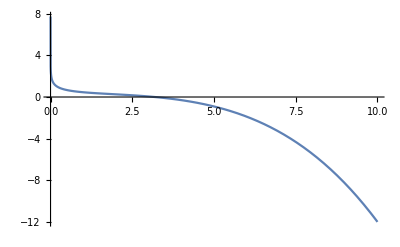

```mathematica
Show[Plot[approx[x],{x,0,10},PlotRange->All],Plot[wolfram[x],{x,0,10},PlotRange-> All]]
```

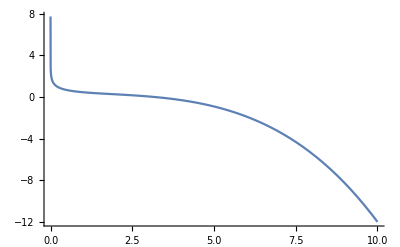

```mathematica
Plot[wolfram[x],{x,0,10},PlotRange-> All]
```

```mathematica
Table[wolfram[x],{x,0.051,10,1}](*we calculate specifically right after x=0, as we have an asymptotic behaviour near that point*)
```

{1.29721,0.431683,0.240708,0.025097,-0.348195,-0.990555,-2.01605,-3.54518,-5.70526,-8.63014}

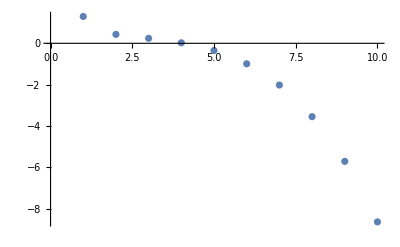

```mathematica
ListPlot[%]
```